```mathematica
X1  = {X,Y,Z};
```

```mathematica
X2 = {x,y,z};
```

```mathematica
RotatedX = EulerMatrix[{α,β,γ}].X2
```

{z Cos[α] Sin[β]+y (-Cos[γ] Sin[α]-Cos[α] Cos[β] Sin[γ])+x (Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ]),z Sin[α] Sin[β]+x (Cos[β] Cos[γ] Sin[α]+Cos[α] Sin[γ])+y (Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ]),z Cos[β]-x Cos[γ] Sin[β]+y Sin[β] Sin[γ]}

```mathematica
eq = {X1[[1]]==RotatedX[[1]],X1[[2]]==RotatedX[[2]],X1[[3]]==RotatedX[[3]]} //Simplify
```

{X+y Cos[γ] Sin[α]+x Sin[α] Sin[γ]==Cos[α] (z Sin[β]+Cos[β] (x Cos[γ]-y Sin[γ])),Y==z Sin[α] Sin[β]+Cos[α] (y Cos[γ]+x Sin[γ])+Cos[β] Sin[α] (x Cos[γ]-y Sin[γ]),Z+x Cos[γ] Sin[β]==z Cos[β]+y Sin[β] Sin[γ]}

```mathematica
eq[[1]]
eq[[2]]
eq[[3]]
```

X+y Cos[γ] Sin[α]+x Sin[α] Sin[γ]==Cos[α] (z Sin[β]+Cos[β] (x Cos[γ]-y Sin[γ]))

Y==z Sin[α] Sin[β]+Cos[α] (y Cos[γ]+x Sin[γ])+Cos[β] Sin[α] (x Cos[γ]-y Sin[γ])

Z+x Cos[γ] Sin[β]==z Cos[β]+y Sin[β] Sin[γ]

```mathematica
Solve[eq,{α,β,γ}]
```

{}

```mathematica
EulerMatrix[{α,β,γ}]//MatrixForm
```

(Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ] | -Cos[γ] Sin[α]-Cos[α] Cos[β] Sin[γ] | Cos[α] Sin[β]
Cos[β] Cos[γ] Sin[α]+Cos[α] Sin[γ] | Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ] | Sin[α] Sin[β]
-Cos[γ] Sin[β] | Sin[β] Sin[γ] | Cos[β])

```mathematica
Jeq = {Sin[θJN]Cos[ϕJN],Sin[θJN]Sin[ϕJN],Cos[θJN]};
JSF = {Sin[θJNSF]Cos[ϕJNSF],Sin[θJNSF]Sin[ϕJNSF],Cos[θJNSF]};
```

```mathematica
v = Cross[Jeq,JSF]//Simplify
```

{Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF],-Cos[θJNSF] Cos[ϕJN] Sin[θJN]+Cos[θJN] Cos[ϕJNSF] Sin[θJNSF],-Sin[θJN] Sin[θJNSF] Sin[ϕJN-ϕJNSF]}

```mathematica
s = √(v.v)//Simplify
```

√(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2))

```mathematica
c = Jeq.JSF//Simplify
```

Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]

```mathematica
V = {{0,-v[[3]],v[[2]]},{v[[3]],0,-v[[1]]},{-v[[2]],v[[1]],0}}
```

{{0,Sin[θJN] Sin[θJNSF] Sin[ϕJN-ϕJNSF],-Cos[θJNSF] Cos[ϕJN] Sin[θJN]+Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]},{-Sin[θJN] Sin[θJNSF] Sin[ϕJN-ϕJNSF],0,-Cos[θJNSF] Sin[θJN] Sin[ϕJN]+Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]},{Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF],Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF],0}}

```mathematica
R = IdentityMatrix[3]+V + V.V(1-c)/s^2//FullSimplify
```

{{1+((-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) ((Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF])^2+Sin[θJN]^2 Sin[θJNSF]^2 Sin[ϕJN-ϕJNSF]^2))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2)),Sin[θJN] Sin[θJNSF] Sin[ϕJN-ϕJNSF]+((Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]) (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) (Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2)),-Cos[θJNSF] Cos[ϕJN] Sin[θJN]+Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]+(Sin[θJN] Sin[θJNSF] (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) Sin[ϕJN-ϕJNSF] (Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2))},{-Sin[θJN] Sin[θJNSF] Sin[ϕJN-ϕJNSF]+((Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]) (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) (Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2)),1+((-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) (Cos[θJNSF]^2 Sin[θJN]^2 Sin[ϕJN]^2-2 Cos[θJN] Cos[θJNSF] Sin[θJN] Sin[θJNSF] Sin[ϕJN] Sin[ϕJNSF]+Sin[θJNSF]^2 (Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2+Cos[θJN]^2 Sin[ϕJNSF]^2)))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2)),-Cos[θJNSF] Sin[θJN] Sin[ϕJN]-(Sin[θJN] Sin[θJNSF] (Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]) (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) Sin[ϕJN-ϕJNSF])/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2))+Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]},{Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]+(Sin[θJN] Sin[θJNSF] (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) Sin[ϕJN-ϕJNSF] (Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2)),Cos[θJNSF] Sin[θJN] Sin[ϕJN]-(Sin[θJN] Sin[θJNSF] (Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]) (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) Sin[ϕJN-ϕJNSF])/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2))-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF],1+(-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF])/(1+Sin[ϕJN-ϕJNSF]/(-2 Cot[θJN] Cot[θJNSF] Cot[ϕJN-ϕJNSF]+(Cot[θJN]^2+Cot[θJNSF]^2) Csc[ϕJN-ϕJNSF]))}}

```mathematica
Assumptions-> {ι∈ {0,2π},A∈ Re, B∈Re, c∈Re, d∈Re}
```

Assumptions→{ι∈{0,2 π},A∈Re,B∈Re,c∈Re,d∈Re}

```mathematica
sols =Simplify[Solve[Sin[ι]A + Sin[ι]B + Cos[ι] c == Cos[θ],Sin[theta]^2 == Cross[J,n].Cross[J,n],{ι}],Assumptions->{C[1]∈ Integers}]
```

Solve[Cos[θ]==c Cos[ι]+(A+B) Sin[ι],Sin[theta]^2==(A-B)^2 Sin[ι]^2+(A Cos[ι]-c Sin[ι])^2+(B Cos[ι]-c Sin[ι])^2,{ι}]

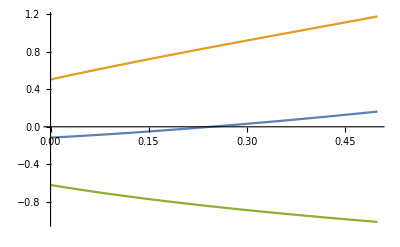

```mathematica
Plot[{ι/.sols[[1]]/.c->√(1-A^2+B^2)/.B->.2/.d->.99/.C[1]->0,ι/.sols[[2]]/.c->√(1-A^2+B^2)/.B->.2/.d->.99/.C[1]->0,(ι/.sols[[1]]/.c->√(1-A^2+B^2)/.B->.2/.d->.99/.C[1]->0 )-(ι/.sols[[2]]/.c->√(1-A^2+B^2)/.B->.2/.d->.99/.C[1]->0)},{A,0,.5}]
```

```mathematica
(ι/.sols[[1]]/.c->√(1-A^2+B^2)/.B->.6/.d->.9/.C[1]->0 )-(ι/.sols[[2]]/.c->√(1-A^2+B^2)/.B->.6/.d->.9/.C[1]->0)/.A->.2 //N
```

-1.74515

```mathematica
J = {A,B,c};
n = {Sin[ι], Sin[ι],Cos[ι]};
```

```mathematica
Cross[J,n].Cross[J,n]
```

(A Sin[ι]-B Sin[ι])^2+(B Cos[ι]-c Sin[ι])^2+(-A Cos[ι]+c Sin[ι])^2

```mathematica
Simplify[Solve[Sin[θ]^2== Cross[J,n].Cross[J,n],{ι}],Assumptions->C[1]∈Integers]
```

{{ι→ArcTan[1/((A+B) c (A^2+B^2-Sin[θ]^2))√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2))) (A^2 c^2+2 A B c^2+B^2 c^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4))),√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2)))]+2 π C[1]},{ι→ArcTan[-1/((A+B) c (A^2+B^2-Sin[θ]^2))√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2))) (A^2 c^2+2 A B c^2+B^2 c^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4))),-√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2)))]+2 π C[1]},{ι→ArcTan[1/((A+B) c (A^2+B^2-Sin[θ]^2))(A^2 c^2+2 A B c^2+B^2 c^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4))) √((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2))),√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2)))]+2 π C[1]},{ι→ArcTan[-1/((A+B) c (A^2+B^2-Sin[θ]^2))(A^2 c^2+2 A B c^2+B^2 c^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4))) √((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2))),-√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2)))]+2 π C[1]}}

```mathematica
LSF = {0,0,1};
NSF = {Sin[ι]Cos[π/2-ϕref],Sin[ι]Sin[π/2 - ϕref],Cos[ι]};
LEQ = {Sin[θl]Cos[ϕl],Sin[θl]Sin[ϕl],Cos[θl]};
NEQ = {Sin[θs]Cos[ϕs],Sin[θs]Sin[ϕs],Cos[θs]};
KSF = Cross[LSF,NSF];
KEQ = Cross[LEQ,NEQ];
JSF = {Jx,Jy,Jz};
```

```mathematica
A = Transpose[{LSF,NSF,KSF}];
B = Transpose[{LEQ,NEQ,KEQ}];
```

```mathematica
MatrixForm[R = B.Inverse[A]//Simplify]
```

(-Csc[ι] (Cos[θs] Cos[ϕref] Sin[θl] Sin[ϕl]+Cos[ι] Cos[ϕl] Sin[θl] Sin[ϕref]-Sin[θs] (Cos[ϕs] Sin[ϕref]+Cos[θl] Cos[ϕref] Sin[ϕs])) | -Csc[ι] (Cos[ι] Cos[ϕl] Cos[ϕref] Sin[θl]-Cos[ϕref] Cos[ϕs] Sin[θs]+Sin[ϕref] (-Cos[θs] Sin[θl] Sin[ϕl]+Cos[θl] Sin[θs] Sin[ϕs])) | Cos[ϕl] Sin[θl]
Csc[ι] (Cos[θs] Cos[ϕl] Cos[ϕref] Sin[θl]-Cos[θl] Cos[ϕref] Cos[ϕs] Sin[θs]+Sin[ϕref] (-Cos[ι] Sin[θl] Sin[ϕl]+Sin[θs] Sin[ϕs])) | -Csc[ι] (Cos[ι] Cos[ϕref] Sin[θl] Sin[ϕl]+Cos[θs] Cos[ϕl] Sin[θl] Sin[ϕref]-Sin[θs] (Cos[θl] Cos[ϕs] Sin[ϕref]+Cos[ϕref] Sin[ϕs])) | Sin[θl] Sin[ϕl]
Csc[ι] ((Cos[θs]-Cos[θl] Cos[ι]) Sin[ϕref]+Cos[ϕref] Sin[θl] Sin[θs] Sin[ϕl-ϕs]) | Csc[ι] (Cos[θs] Cos[ϕref]-Cos[θl] Cos[ι] Cos[ϕref]-Sin[θl] Sin[θs] Sin[ϕref] Sin[ϕl-ϕs]) | Cos[θl])

```mathematica
MatrixForm[R.JSF//FullSimplify]
```

(Cos[ϕl] Sin[θl] (Jz-Cot[ι] (Jy Cos[ϕref]+Jx Sin[ϕref]))+Csc[ι] (Cos[ϕref] (Jy Cos[ϕs] Sin[θs]-Jx Cos[θs] Sin[θl] Sin[ϕl]+Jx Cos[θl] Sin[θs] Sin[ϕs])+Sin[ϕref] (Jx Cos[ϕs] Sin[θs]+Jy Cos[θs] Sin[θl] Sin[ϕl]-Jy Cos[θl] Sin[θs] Sin[ϕs]))
Jz Sin[θl] Sin[ϕl]+Cos[θs] Cos[ϕl] Csc[ι] Sin[θl] (Jx Cos[ϕref]-Jy Sin[ϕref])+Cos[θl] Cos[ϕs] Csc[ι] Sin[θs] (-Jx Cos[ϕref]+Jy Sin[ϕref])-(Jy Cos[ϕref]+Jx Sin[ϕref]) (Cot[ι] Sin[θl] Sin[ϕl]-Csc[ι] Sin[θs] Sin[ϕs])
Cos[θl] (Jz-Cot[ι] (Jy Cos[ϕref]+Jx Sin[ϕref]))+Csc[ι] (Cos[θs] (Jy Cos[ϕref]+Jx Sin[ϕref])+Sin[θl] Sin[θs] (Jx Cos[ϕref]-Jy Sin[ϕref]) Sin[ϕl-ϕs]))

```mathematica
LSFn = {0,0,1};
NSFn = {si cp,si sp,ci};(*Direction of GW propagation ι is the angle between line of sight and L, not vector to source and L*)
LEQn = {stl cpl,stl spl,ctl};
NEQn = {-sts cps,-sts sps,-cts};(*Direction of GW propagation -- (-) sign comes from using line of sight, not source vector*)
KSFn = Cross[LSFn,NSFn]
KEQn = Cross[LEQn,NEQn]
JSFn = {Jxn,Jyn,Jzn};
```

{-si sp,cp si,0}

{-cts spl stl+ctl sps sts,cpl cts stl-cps ctl sts,cps spl stl sts-cpl sps stl sts}

```mathematica
An = Transpose[{LSFn,NSFn,KSFn}];
Bn = Transpose[{LEQn,NEQn,KEQn}];
MatrixForm[Rn = Bn.Inverse[An]//Simplify]
```

(-(ci cp cpl stl-cts sp spl stl+cp cps sts+ctl sp sps sts)/(cp^2 si+si sp^2) | -(ci cpl sp stl+cp cts spl stl+cps sp sts-cp ctl sps sts)/(cp^2 si+si sp^2) | cpl stl
-(cpl cts sp stl+ci cp spl stl-cps ctl sp sts+cp sps sts)/(cp^2 si+si sp^2) | (cp cpl cts stl-ci sp spl stl-cp cps ctl sts-sp sps sts)/(cp^2 si+si sp^2) | spl stl
-(ci cp ctl+cp cts+sp (cps spl-cpl sps) stl sts)/(si (cp^2+sp^2)) | -(ci ctl sp+cts sp+cp (-cps spl+cpl sps) stl sts)/(si (cp^2+sp^2)) | ctl)

```mathematica
MatrixForm[JEQ = Simplify[Rn.JSFn]/.cp^2+sp^2->1]
```

((cp^2 cpl Jzn si stl-ci cpl (cp Jxn+Jyn sp) stl-cp (cts Jyn spl stl+cps Jxn sts-ctl Jyn sps sts)+sp (cpl Jzn si sp stl+cts Jxn spl stl-(cps Jyn+ctl Jxn sps) sts))/si
(cp^2 Jzn si spl stl+sp (-cpl cts Jxn stl-ci Jyn spl stl+Jzn si sp spl stl+cps ctl Jxn sts-Jyn sps sts)+cp (cpl cts Jyn stl-ci Jxn spl stl-(cps ctl Jyn+Jxn sps) sts))/si
(ctl Jzn si-Jxn (ci cp ctl+cp cts+sp (cps spl-cpl sps) stl sts)-Jyn (ci ctl sp+cts sp+cp (-cps spl+cpl sps) stl sts))/si)

```mathematica
CForm[JEQ[[1]]]
```

(Power(cp,2)*cpl*Jzn*si*stl - ci*cpl*(cp*Jxn + Jyn*sp)*stl - cp*(cts*Jyn*spl*stl + cps*Jxn*sts - ctl*Jyn*sps*sts) + 
     sp*(cpl*Jzn*si*sp*stl + cts*Jxn*spl*stl - (cps*Jyn + ctl*Jxn*sps)*sts))/si

```mathematica
CForm[JEQ[[2]]]
```

(Power(cp,2)*Jzn*si*spl*stl + sp*(-(cpl*cts*Jxn*stl) - ci*Jyn*spl*stl + Jzn*si*sp*spl*stl + cps*ctl*Jxn*sts - Jyn*sps*sts) + 
     cp*(cpl*cts*Jyn*stl - ci*Jxn*spl*stl - (cps*ctl*Jyn + Jxn*sps)*sts))/si

```mathematica
CForm[JEQ[[3]]]
```

(ctl*Jzn*si - Jxn*(ci*cp*ctl + cp*cts + sp*(cps*spl - cpl*sps)*stl*sts) - Jyn*(ci*ctl*sp + cts*sp + cp*(-(cps*spl) + cpl*sps)*stl*sts))/si

```mathematica
(*Testing*)
```

```mathematica
m1 = 4;
m2 = 2;
m = m1+m2;
eta = m1*m2/m^2;
chi1sf = .1;
chi2sf = .1;
chip = .8;
phip = .2;
x = ( 20*(m1+m2)*1.5*^-6  π)^(2/3);
L = (eta*(1.0+(1.5+eta/6.0)*x+(3.375-(19.0*eta)/8.-eta*eta/24.0)*x*x))/Sqrt[(x)]
Jx = m1*m1*chip*Cos[phip]
Jy =m1*m1* chip*Sin[phip]
Jz = m*m*L + chi1sf*m1*m1 + chi2sf*m2*m2
Jsf = {Jx,Jy,Jz};
chi1eq = Rn.{0,0,chi1sf};
chi2eq = Rn.{0,0,chi2sf};
chipeq = Rn.{chip * Cos[phip],chip * Sin[phip],0}//Simplify;
Leq = Rn.{0,0,L};
Jeq = chi1eq*m1*m1+chi2eq*m2*m2+chipeq*m1*m1+Leq*m*m//Simplify;
Jeqrot = Rn.Jsf//Simplify;
Leq = {stl cpl, stl spl, ctl};
Jeqrot.Leq//Simplify
```

2.71589

12.5449

2.54297

99.7719

1/(si (cp^2+sp^2))(0.+2.54297 ctl cts sp+99.7719 ctl^2 si sp^2+99.7719 cpl^2 si sp^2 stl^2+99.7719 si sp^2 spl^2 stl^2+ci (-12.5449 cp ctl^2-2.54297 ctl^2 sp+cp (-12.5449 cpl^2-12.5449 spl^2) stl^2+sp (-2.54297 cpl^2-2.54297 spl^2) stl^2)+cp^2 si (99.7719 ctl^2+(99.7719 cpl^2+99.7719 spl^2) stl^2)+2.54297 cpl cps sp stl sts-3.55271×10^-15 cps ctl sp spl stl sts+3.55271×10^-15 cpl ctl sp sps stl sts+2.54297 sp spl sps stl sts+cp (12.5449 ctl cts+(12.5449 cpl cps+12.5449 spl sps) stl sts))

```mathematica
(*Self consistent at least*)
Jeq - Jeqrot//FullSimplify//MatrixForm
```

(0.
(0.-1.77636×10^-15 cpl cts sp stl+1.77636×10^-15 cps ctl sp sts)/(cp^2 si+si sp^2)
0.)

```mathematica
(*Equatorial to Ecliptic -- Rotation about x by axial_tilt*)
```

```mathematica
eclvec = {Sin[thetaecl]Cos[phiecl],Sin[thetaecl]Cos[phiecl],Cos[thetaecl]}; 
eclvec = {x,y,z}; 
eqvec = {Sin[thetaeq]Cos[phieq],Sin[thetaeq]Cos[phieq],Cos[thetaeq]};
```

```mathematica
roteq = {{1,0,0},{0,Cos[TILT],Sin[TILT]},{0, -Sin[TILT],Cos[TILT]}}.eqvec/.TILT->23.44π/180//Simplify
```

{Cos[phieq] Sin[thetaeq],0.397789 Cos[thetaeq]+0.917477 Cos[phieq] Sin[thetaeq],0.917477 Cos[thetaeq]-0.397789 Cos[phieq] Sin[thetaeq]}

```mathematica
eqs = {eclvec[[1]]==roteq[[1]], eclvec[[2]]==roteq[[2]].eclvec[[3]]==roteq[[3]]}
```

{True,-0.397789 Cos[thetaeq]+0.917477 Cos[phieq] Sin[thetaeq]==(-0.397789 Cos[thetaeq]+0.917477 Cos[phieq] Sin[thetaeq]).(0.917477 Cos[thetaeq]+0.397789 Cos[phieq] Sin[thetaeq])==0.917477 Cos[thetaeq]+0.397789 Cos[phieq] Sin[thetaeq]}

```mathematica
x = roteq[[1]];
y = roteq[[2]];
z = roteq[[3]];
```

```mathematica
phiecl = ArcTan[y,x]
thetaecl = ArcTan[(√(x*x + y y))/z]
```

ArcTan[0.397789 Cos[thetaeq]+0.917477 Cos[phieq] Sin[thetaeq],Cos[phieq] Sin[thetaeq]]

ArcTan[(√(Cos[phieq]^2 Sin[thetaeq]^2+(0.397789 Cos[thetaeq]+0.917477 Cos[phieq] Sin[thetaeq])^2))/(0.917477 Cos[thetaeq]-0.397789 Cos[phieq] Sin[thetaeq])]

```mathematica
{(phiecl),(π/2-thetaecl)}/.thetaeq->π/2-23.44π/180 /.phieq-> 60π/180
```

{0.669926,0.242151}